```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

```mathematica
(***************************************************************************************)
(*This notebook is for testing the Dynamics Algorithm using a simple 1-bar mechanism*)
(***************************************************************************************)
```

```mathematica
(*Defining Absolute Coordinates*)
q={x[t],y[t],θ[t]}
```

{x[t],y[t],θ[t]}

```mathematica
(*Defining Constraints*)
Φ = {x[t] - Cos[θ[t]], y[t] - Sin[θ[t]]}
```

{-Cos[θ[t]]+x[t],-Sin[θ[t]]+y[t]}

```mathematica
J= D[Φ,{q}] (* Jacobian Matrix *)
```

{{1,0,Sin[θ[t]]},{0,1,-Cos[θ[t]]}}

```mathematica
q' = D[q, t]
```

{x'[t],y'[t],θ'[t]}

```mathematica
m = 1
M = {{m,0,0},{0,m,0},{0,0,m/3}}
```

1

{{1,0,0},{0,1,0},{0,0,1/3}}

```mathematica
J.q'
```

{x'[t]+Sin[θ[t]] θ'[t],y'[t]-Cos[θ[t]] θ'[t]}

```mathematica
D[(J.q'), {q}]
```

{{0,0,Cos[θ[t]] θ'[t]},{0,0,Sin[θ[t]] θ'[t]}}

```mathematica
Subscript[Q, d]=-(D[(J.q'), {q}]).q'
```

{-Cos[θ[t]] θ'[t]^2,-Sin[θ[t]] θ'[t]^2}

```mathematica
Subscript[Q, e]= {0,0,1}
```

{0,0,1}

```mathematica
MIn = Inverse[M]
```

{{1,0,0},{0,1,0},{0,0,3}}

```mathematica
Jt = Transpose[J]
```

{{1,0},{0,1},{Sin[θ[t]],-Cos[θ[t]]}}

```mathematica
q''=MIn.Subscript[Q, e]+MIn.Jt.(Inverse[J.MIn.Jt].(Subscript[Q, d]-J.MIn.Subscript[Q, e]))
```

{((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),(3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),3+3 Sin[θ[t]] (((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))-3 Cos[θ[t]] ((3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))}

```mathematica
eqns1 = D[D[q, t], t] - q''
```

{-((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+x''[t],-(3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+y''[t],-3-3 Sin[θ[t]] (((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))+3 Cos[θ[t]] ((3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))+θ''[t]}

```mathematica
Subscript[Q, c] = {Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t]} 
eqns2 = Subscript[Q, c] -Jt.Inverse[J.MIn.Jt].(Subscript[Q, d]-J.MIn.Subscript[Q, e])
(*eqns2 = Subscript[Q, c]- (Subscript[Q, e]- M.Inverse[J].Subscript[Q, d])*)
```

{Q_1[t],Q_2[t],Q_3[t]}

{Q_1[t]-((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),Q_2[t]-(3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),Q_3[t]-(-(3 Cos[θ[t]]^2 Sin[θ[t]])/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Cos[θ[t]]^2) Sin[θ[t]])/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2)-((3 Cos[θ[t]] Sin[θ[t]]^2)/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(Cos[θ[t]] (1+3 Sin[θ[t]]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2)}

```mathematica
eqns=Join[eqns1,eqns2]=={0,0,0,0,0,0}
```

{-((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+x''[t],-(3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+y''[t],-3-3 Sin[θ[t]] (((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))+3 Cos[θ[t]] ((3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2))+θ''[t],Q_1[t]-((1+3 Cos[θ[t]]^2) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(3 Cos[θ[t]] Sin[θ[t]] (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),Q_2[t]-(3 Cos[θ[t]] Sin[θ[t]] (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-((1+3 Sin[θ[t]]^2) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2),Q_3[t]-(-(3 Cos[θ[t]]^2 Sin[θ[t]])/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)+((1+3 Cos[θ[t]]^2) Sin[θ[t]])/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)) (-3 Sin[θ[t]]-Cos[θ[t]] θ'[t]^2)-((3 Cos[θ[t]] Sin[θ[t]]^2)/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)-(Cos[θ[t]] (1+3 Sin[θ[t]]^2))/(1+3 Cos[θ[t]]^2+3 Sin[θ[t]]^2)) (3 Cos[θ[t]]-Sin[θ[t]] θ'[t]^2)}=={0,0,0,0,0,0}

```mathematica
(* s=NDSolve[{eqns,x[0]==1,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0},{x,y,θ},{t,0,10}] *)
s=NDSolve[{eqns,x[0]==1,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0},Join[q, Subscript[Q, c]],{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t],θ[t]→InterpolatingFunction[{{0.,10.}},<>][t],Q_1[t]→InterpolatingFunction[{{0.,10.}},<>][t],Q_2[t]→InterpolatingFunction[{{0.,10.}},<>][t],Q_3[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

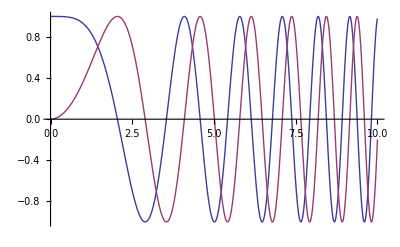

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,0,10},PlotStyle->Automatic]
```

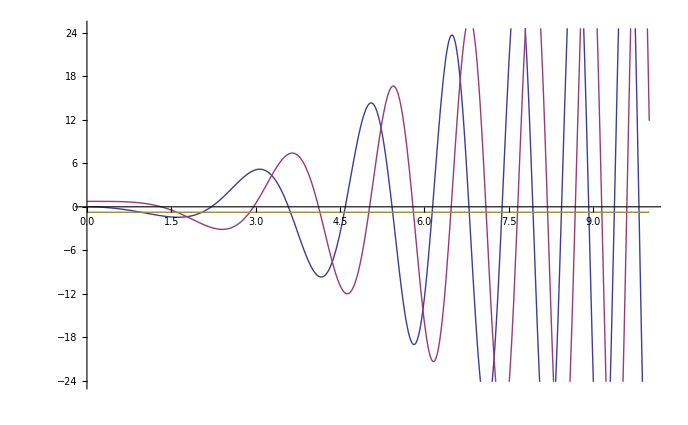

```mathematica
Plot[Evaluate[{Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t]}/.s],{t,0,10},PlotStyle->Automatic]
```